```mathematica
me=9.10938*10^-28
h=6.626*10^-27
c=2.998*10^10
me c^2/h
c/%
h/(me c)
```

9.10938×10^-28

6.626×10^-27

2.998×10^10

1.23566×10^20

2.42622×10^-10

2.42622×10^-10

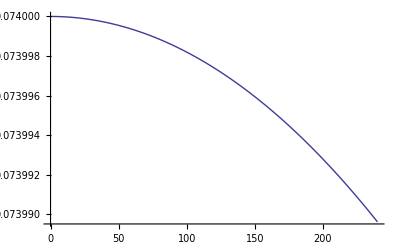

1.76075×10^-11 ν

1.7706×10^-23

(ⅇ^x x^4)/((-1+ⅇ^x)^2)

-(6.83609×10^-47 ⅇ^(1.76075×10^-11 ν) ν^4)/((-1+ⅇ^(1.76075×10^-11 ν))^2)

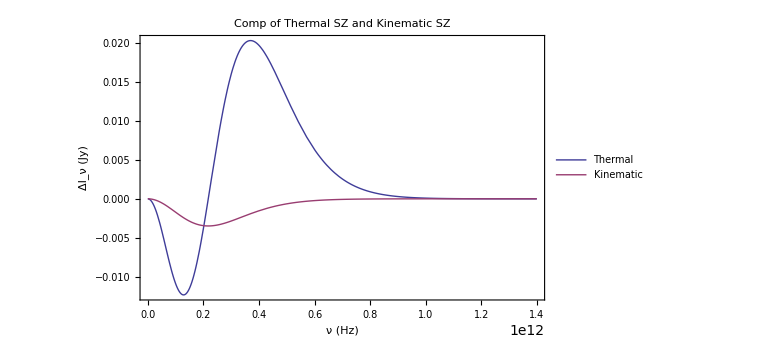

```mathematica
Remove["Global`*"]
h=4.136*10^-15 ;
k=8.617*10^-5 ;
To=2.726 ;
c=2.998*10^10 ;
mec2=.5*10^6;
kT={5,10,15}*10^3 ;
σT=.665*10^-24 ;

g[x_]=(x^4 Exp[x])/(Exp[x]-1)^2((x(Exp[x]+1))/(Exp[x]-1)-4);
io=(2 (k To)^3)/(h c)^2;
y=kT/mec2;
ΔI= y g[x] ;
(*
Plot[ΔI,{x,0,14},Frame->True,PlotStyle->Thick,PlotLegends->{"5 eV","10 eV","15 eV"},FrameLabel->{"x","ΔI/(τ io)"},PlotLabel->"Spectral Dependence of ΔI"]*)
ne[r_]=(.074)/((1+(r/17000)^2)^(3(.47)/2));
Plot[ne[r],{r,0,240}]
τ= σT Integrate[ne[r],{r,0,240*10^6}];
T=((3.83 k)/(h 217 10^9))^-1;
xo=(h ν)/(k To)

yH=(3.5*10^3)/mec2 τ
hf[x_]=x^4 Exp[x]/(Exp[x]-1)^2
Vr=500 *10^5;
ΔIk=-io (hf[xo]Vr τ)/c 10^23
Plot[{io g[xo]yH  10^23,-io hf[xo]Vr τ/c 10^23},{ν,0,14 10^11},Frame->True,FrameLabel->{"ν (Hz)","ΔI_ν (Jy)"},Exclusions->None,Axes->False,PlotRange->All,ImageSize->Large,PlotLabel->"Comp of Thermal SZ and Kinematic SZ",PlotLegends->{"Thermal","Kinematic"}]
```

```mathematica
Remove["Global`*"]
Δϵ=(ϵ γ^2(1-β)^2)/(1+(2 ϵ γ(1-β))/(m c^2))-ϵ
Assuming[0<β<1&&γ>0&&c>0&&m>0,FullSimplify[D[Δϵ,ϵ]]]
Solve[%==0,ϵ][[2]]
Assuming[0<β<1&&γ>0&&c>0&&m>0,FullSimplify[(Δϵ/.% )]]
Assuming[0<β<1&&γ>0&&c>0&&m>0,FullSimplify[(Δϵ/.%% )-(γ-1)m c^2]]
```

-ϵ+((1-β)^2 γ^2 ϵ)/(1+(2 (1-β) γ ϵ)/(c^2 m))

-1+(c^4 m^2 (-1+β)^2 γ^2)/((c^2 m-2 (-1+β) γ ϵ)^2)

{ϵ→(c^2 m (1-γ+β γ))/(2 (-1+β) γ)}

-(m (c+c (-1+β) γ)^2)/(2 (-1+β) γ)

-(c^2 m (1+(-1+β^2) γ^2))/(2 (-1+β) γ)

1.6

3.2

ϵ^((1-p)/2)

1584.89

Piecewise[{{1/ϵ^0.3, ϵ≤10000}, {1584.89/ϵ^1.1, ϵ≥10000}, {0, True}}]

1/ϵ^0.7

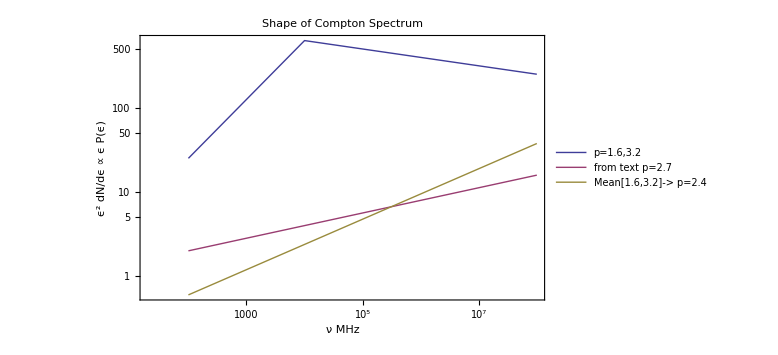

```mathematica
Remove["Global`*"]
p1=1.6
p2=3.2
P1[ϵ_,p_]= ϵ^(-(p-1)/2) //Simplify
B=B/.Solve[P1[10^4,p1]==B P1[10^4,p2]][[1]]
spec[ϵ_]=Piecewise[{{P1[ϵ,p1], ϵ<=10^4}, {B P1[ϵ,p2], ϵ>=10^4}}]
P1[ϵ,2.4]
LogLogPlot[{ ϵ spec[ϵ],ϵ^2 ϵ^-1.85,.15 ϵ P1[ϵ,2.4]},{ϵ,10^2,10^8},AxesOrigin->{20,10},PlotStyle->Thick,Frame->True,FrameLabel->{"ν MHz",Style[" ϵ^2 dN/dϵ ∝ ϵ P(ϵ)",15]},PlotLabel->"Shape of Compton Spectrum",PlotLegends->{"p=1.6,3.2","from text p=2.7","Mean[1.6,3.2]-> p=2.4"},Exclusions->None,ImageSize->Large]
```

```mathematica
(2-1.85)*2+1
```

1.3